NB: Sending χ→-χ to flip plot the right way round

I have begun deleting old plot commands, see GitHub for previous commits.

```mathematica
(*Using the same values as Fig.3 in Korobko et al, 2019: benchmark 3rd generation detector*)
c=3. 10^8(*ms^-1*);
ℏ=1. 10^-34(*Js*);
λ=1550. 10^-9(*m*);
w0=2π c/λ;
P = 4. 10^6(*W*);
Larm=20. 10^3(*m*);
Lse=56.(*m*);
Titm=0.07;
Tse=0.35;
ws=c(Titm/(4 Lse Larm))^(1/2);(*to-do: figure out if this formula is just a low loss approximation, as suspected by Min Jet Yap*)
Print[StringForm["ω_s<<ω_FSR?: ω_s=``, ω_FSR=``",ws,c/(2 Larm)]]
τRoundTripSE=(2Lse)/c;
γ=-1/(2 τRoundTripSE)Log[1-Tse]; (*Subscript[γ, R]=-1/(2 τRoundTripSE)Log[1-Tse]≃Tse/(2 τRoundTripSE)=(c Tse)/(4 Lse),*)
kout=γ;
G=((2P Larm w0)/(ℏ c))^(1/2);
(*the authors don't say what value they use for χ, threshold?*)
Sh[Ω_,χ_]:=(ℏ c)/(8 P Larm w0)(Ω^2(γ-χ)^2+(ws^2-Ω^2)^2)/(ws^2 γ)
ASDh[Ω_,χ_]:=Abs[Sh[Ω,χ]]^(1/2)
(*LogLogPlot[{ASDh[Ω,χ=0],ASDh[Ω,χ=0.5γ],ASDh[Ω,χ=0.7γ],ASDh[Ω,χ=0.9γ],ASDh[Ω,χ=0.95γ],ASDh[Ω,χ=γ]},{Ω,10,10^5},AxesLabel->{"angular freq / Hz (log scale)", "strain sensitivity (NSR) / Hz^(-1/2) (log scale)"},ImageSize->Large,PlotRange->All,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless degenerate internal squeezing - different parametric gains\nNB: factor of two corrected using S_vac=2 for single-sided PSD w quadrature normalisation"]*)
Print["[old plot commented out]"]
```

ω_s<<ω_FSR?: ω_s=37500., ω_FSR=7500

[old plot commented out]

```mathematica
(*checking other quadrature, noise transfer function is the same as before, just with χ->-χ*)

R2Lossy[Ω_,χ_,lossRatio_]:=(1+(4 Ω^2 kout χ)/(Ω^2(kout+(kout*lossRatio)/(1-lossRatio)-χ)^2+(ws^2-Ω^2)^2))^(1/2)
(*
Labeled[LogLinearPlot[{
20Log10[RLossy[2π f,χ=kout,lossRatio=0.1]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0.03]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0.005]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0]],
20Log10[R2Lossy[2π f,χ=kout,lossRatio=0.1]],
20Log10[R2Lossy[2π f,χ=kout,lossRatio=0.03]],
20Log10[R2Lossy[2π f,χ=kout,lossRatio=0.005]],
20Log10[R2Lossy[2π f,χ=kout,lossRatio=0]]},{f,10,10^5},ImageSize->400,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossy degenerate internal squeezing\ndifferent optical losses\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector\nshowing both quadratures\nsee that optical loss affects the squeezed quadrature more,\njust like a degenerate OPO",PlotStyle->{,,,,Dashed,Dashed,Dashed,Dashed},PlotRange->{{10,10^5},{-60,60}}],{"frequency, f=Ω/(2 π) / Hz (log scale)","strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
*)
Print["[old plot omitted]"]
```

[old plot omitted]

```mathematica
(*external squeezing injected into conventional detector*)
(*pulling values from Wade et al, 2016 - https://aip.scitation.org/doi/pdf/10.1063/1.4953326*)
Clear[Rpd]
TExt=0.155;
LExt=0.18;(*m*)
τRoundTripExt=(2 LExt)/c;
κafExt=-1/(2 τRoundTripExt)Log[1-TExt];(*aka. κaoutExt*)
(*now quoting losses as Subscript[T, l], transmitivity (of power/energy) of loss port mirror, instead of using loss ratio=1-ηesc*)
κaExt[TlExt_]:=κafExt+-1/(2 τRoundTripExt)Log[1-TlExt]
VExt[Ω_,gExt_,Rinj_,TlExt_]:=1-(4 κafExt gExt)/((κaExt[TlExt]+gExt)^2+Ω^2)(1-Rinj)
τRoundTripArm=(2 Larm)/c;
τRoundTripSE=(2 Lse)/c;
κa[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla];
κaqout=kout;
κaq[Tlaq_]:=κaqout+-1/(2 τRoundTripSE)Log[1-Tlaq];
RIntExtSqz[Ω_,χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_]:=((1-Rpd)(
VExt[Ω,gExt,Rinj,TlExt] Abs[(2κaqout-κaq[Tlaq]-χ+I Ω-ws^2/(κa[Tla]-I Ω))/(κaq[Tlaq]+χ-I Ω+ws^2/(κa[Tla]-I Ω))]^2
+Abs[(2(κaqout (κaq[Tlaq]-κaqout))^(1/2))/(κaq[Tlaq]+χ-I Ω+ws^2/(κa[Tla]-I Ω))]^2
+Abs[(2(κaqout κa[Tla])^(1/2)ws)/((κaq[Tlaq]+χ-I Ω)(κa[Tla]-I Ω)+ws^2)]^2)+Rpd)^(1/2)
TIntExtSqz[Ω_,χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_]:=(1-Rpd)^(1/2)Abs[(2 (κaqout)^(1/2)ws G)/((κaq[Tlaq]+χ-I Ω)(κa[Tla]-I Ω)+ws^2)]
ASDShIntExtSqz[Ω_,χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_]:=(1/(4 κaqout ws^2 G^2)(
VExt[Ω,gExt,Rinj,TlExt](((2κaqout-κaq[Tlaq]-χ)κa[Tla]+Ω^2-ws^2)^2
						+Ω^2(κa[Tla]-(2κaqout-κaq[Tlaq]-χ))^2)
+(κa[Tla]^2+ Ω^2)4κaqout (κaq[Tlaq]-κaqout)
+4κaqout κa[Tla] ws^2
+ Rpd/(1-Rpd)(((-κaq[Tlaq]-χ)κa[Tla]+Ω^2-ws^2)^2
		+Ω^2(κa[Tla]-(-κaq[Tlaq]-χ))^2)))^(1/2)
```

```mathematica
(*automated plotting, just enter values into valsList*)
unpackRIntExtSqz[Ω_,vals_]:=RIntExtSqz[Ω,vals[[1]],vals[[2]],vals[[3]],vals[[4]],vals[[5]],vals[[6]],vals[[7]]]
unpackTIntExtSqz[Ω_,vals_]:=TIntExtSqz[Ω,vals[[1]],vals[[2]],vals[[3]],vals[[4]],vals[[5]],vals[[6]],vals[[7]]]
unpackASDShIntExtSqz[Ω_,vals_]:=ASDShIntExtSqz[Ω,vals[[1]],vals[[2]],vals[[3]],vals[[4]],vals[[5]],vals[[6]],vals[[7]]]
(*each vals contains: {χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_}*)
labeller[vals_]:=(
paddedStrings=StringPadRight[{
ToString[N[vals[[1]]/κaqout]],
ToString[N[vals[[2]]/κafExt]],
ToString[N[vals[[3]]]],
ToString[N[vals[[4]]]],
ToString[N[vals[[5]]]],
ToString[N[vals[[6]]]],
ToString[N[vals[[7]]]]},4];
Style[If[vals[[2]]==0,
StringForm["χ/κ_a_q=``; T_(l, a)=``, T_(l, SubscriptBox[a, q])=``, R_PD=``",
paddedStrings[[1]],
paddedStrings[[3]],
paddedStrings[[4]],
paddedStrings[[5]]],
StringForm["χ/κ_a_q=`1`; T_(l, a)=`3`, T_(l, SubscriptBox[a, q])=`4`, R_PD=`5`; g_ext/κ_(af, ext)=`2`, T_(l, ext)=`7`, R_inj=`6`",
paddedStrings[[1]],
paddedStrings[[2]],
paddedStrings[[3]],
paddedStrings[[4]],
paddedStrings[[5]],
paddedStrings[[6]],
paddedStrings[[7]]]],FontFamily->"Monospace"])

plotIntExtSqz[valsList_,plotLabel_:"internal/external squeezing",plotStyle_:{},legendLabel_:None,fplotMin_:10,fplotMax_:10^5]:=(
p1=LogLinearPlot[Evaluate[Table[20Log10[unpackRIntExtSqz[2π f,valsList[[i]]]],{i,1,Length[valsList]}]],
{f,fplotMin,fplotMax},ImageSize->350,Frame->True,PlotLegends->LineLegend[Table[labeller[valsList[[i]]],{i,1,Length[valsList]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}},LegendLabel->legendLabel],
ImagePadding->{{100,10},{1,All}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fplotMin,fplotMax},All},PlotStyle->plotStyle,FrameLabel->{{"shot noise transfer function,\n|R| / dB (20log10)",},{,plotLabel}}];
p2=LogLogPlot[Evaluate[Table[unpackTIntExtSqz[2π f,valsList[[i]]],{i,1,Length[valsList]}]],
{f,fplotMin,fplotMax},ImageSize->350,PlotRange->{{fplotMin,fplotMax},All},PlotLegends->LineLegend[Table[labeller[valsList[[i]]],{i,1,Length[valsList]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],
ImagePadding->{{100,10},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"signal transfer function,\n|T| / [?] (log scale)",},{,}}];
p3=LogLogPlot[Evaluate[Join[Table[unpackASDShIntExtSqz[2π f,valsList[[i]]],{i,1,Length[valsList]}],{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],{f,fplotMin,fplotMax},ImageSize->350,PlotRange->{{fplotMin,fplotMax},All},PlotLegends->LineLegend[Join[Table[labeller[valsList[[i]]],{i,1,Length[valsList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],
ImagePadding->{{100,10},{50,1}},Filling->{Length[valsList]+1->Bottom},PlotStyle->If[plotStyle=={},Join[Table[,{n,1,Length[valsList]}],{Directive[DotDashed,Red]}],Join[plotStyle,{Directive[DotDashed,Red]}]],Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",}}];
Column[{p1,p2,p3},Spacings->0])
```

```mathematica
(* external squeezing
(*specify dB of injected squeezing*)
injdB=15(*dB*);
Clear[r]
gExtRatio0=(r/.Minimize[Abs[20Log10[unpackRIntExtSqz[1,{0kout,r κafExt,0,0,0,0,0}]]-(-injdB)],r][[2,1]]);
(*each vals contains: {χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_}*)
valsList0={
{0kout,0κafExt,0,0,0,0,0},
{0kout,gExtRatio0 κafExt,0,0,0,0,0},
{0kout,gExtRatio0 κafExt,0,0,0,0,0.1},
{0kout,gExtRatio0 κafExt,0,0,0,0.5,0},
{0kout,gExtRatio0 κafExt,0.1,0.1,0.5,0.5,0.1}};
plotIntExtSqz[valsList0,"lossy external squeezing\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector"]
*)
```

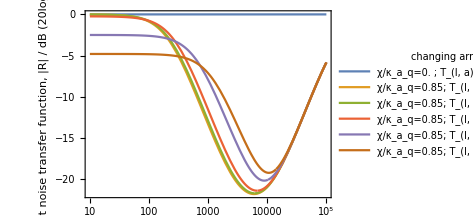
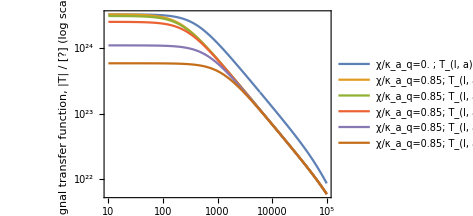
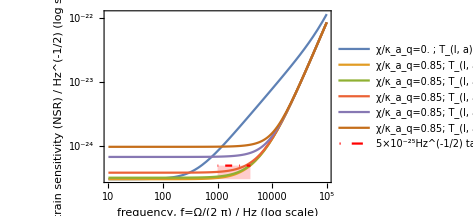

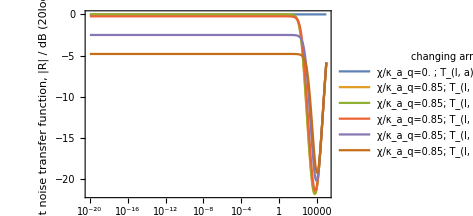
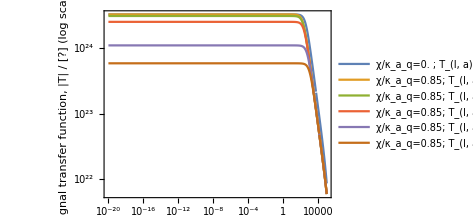
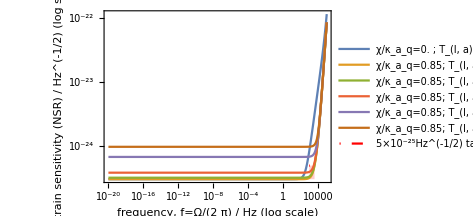

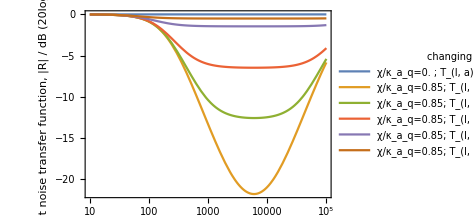
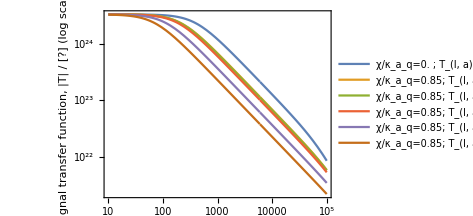

```mathematica
(*setting SRC to be lossless*)
(*each vals contains: {χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_}*)
χRatio0=0.85;
valsList1={
{0kout,0κafExt,0,0,0,0,0},
{χRatio0 kout,0κafExt,0,0,0,0,0},
{χRatio0 kout,0κafExt,0.02,0,0,0,0},
{χRatio0 kout,0κafExt,0.1,0,0,0,0},
{χRatio0 kout,0κafExt,0.5,0,0,0,0},
{χRatio0 kout,0κafExt,0.8,0,0,0,0}};
plotIntExtSqz[valsList1,"lossy degenerate internal squeezing\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector",{},"changing arm cavity intra-cavity loss"]
plotIntExtSqz[valsList1,"lossy degenerate internal squeezing\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector",{},"changing arm cavity intra-cavity loss",10^-20,10^5]
valsList1={
{0kout,0κafExt,0,0,0,0,0},
{χRatio0 kout,0κafExt,0,0,0,0,0},
{χRatio0 kout,0κafExt,0,0.02,0,0,0},
{χRatio0 kout,0κafExt,0,0.1,0,0,0},
{χRatio0 kout,0κafExt,0,0.5,0,0,0},
{χRatio0 kout,0κafExt,0,0.8,0,0,0}};
plotIntExtSqz[valsList1,"lossy degenerate internal squeezing\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector",{},"changing SRC intra-cavity loss"]
```

```mathematica
(*plotting peak shot noise vs arm cavity intra-cavity loss*)
(*Print[StringForm["(raw) sloshing frequency, ω_s/(2 π)=`` Hz",NumberForm[ws/(2π)]]]
Plot[(f/.FindMinimum[{20Log10[unpackRIntExtSqz[2π f,{χRatio0 kout,0κafExt,Tla0,0,0,0,0}]],f>0},f][[2]])/(ws/(2π)),{Tla0,0,1},Frame->True,FrameLabel->{{"shot noise peak frequency error, f/ω_s ",},{"arm cavity intra-cavity loss, T_(l, a)",StringForm["degenerate internal squeezing, χ=``\nshot noise peak frequency vs arm cavity loss\nall other losses zero",χRatio0]}}]*)
-Graphics-;(*result found using NMinimize which is better/slower than FindMinimum*)
(*Plot[(f/.NMinimize[{20Log10[unpackRIntExtSqz[2π f,{χRatio0 kout,0κafExt,0,Tlaq0,0,0,0}]],10<f<10^5},f][[2]])/(ws/(2π)),{Tlaq0,0,1},Frame->True,FrameLabel->{{"shot noise peak frequency, f/ω_s",},{"SRC intra-cavity loss, T_(l, aq)",StringForm["degenerate internal squeezing, χ=``\nshot noise peak frequency vs SRC loss\nall other losses zero",χRatio0]}}]*)
-Graphics-; (*result found using NMinimize which is better/slower than FindMinimum*)(*a strange result -- is any of this physical? behaviour appears to change around T=0.5?*)
```

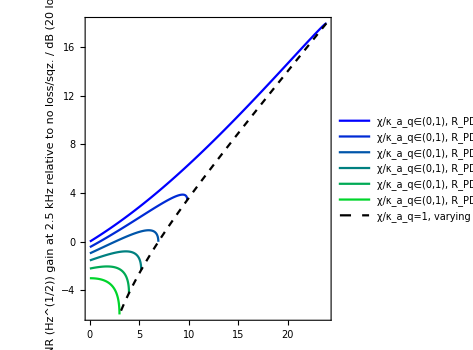
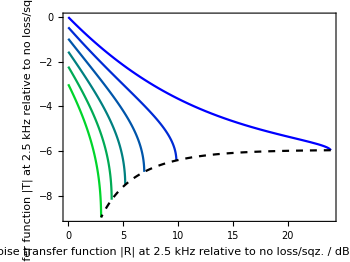

```mathematica
(*the "threshold finding plot":
sensitivity improvement at fProbe vs χ plot, but with no loss in the arms,
the message: the optimum sensitivity moves off the lossless threshold -- i.e. threshold changes with loss*)
fProbe=2.5 10^3(*Hz*);
probeSensRef=unpackASDShIntExtSqz[2π fProbe,{0,0,0,0,0,0,0}] (*everything turned off -> conventional?*);

(*
armLossList={0};(*Range[0,0.5,0.25];*)
srcLossList=Range[0,0.5,0.25];
(*
Plot[Evaluate[Table[20Log10[unpackASDShIntExtSqz[2π fProbe,{2/τRoundTripSE Log[10^(rdB/20)],0,armLossList[[i]],srcLossList[[j]],0,0,0}]/probeSensRef]
,{i,1,Length[armLossList]},{j,1,Length[srcLossList]}]],{rdB,0,5},PlotLegends->LineLegend[Flatten[Table[StringForm["T_(l, a)=``, T_(l, aq)=``",armLossList[[i]],srcLossList[[j]]],{i,1,Length[armLossList]},{j,1,Length[srcLossList]}]],LabelStyle->Directive[10]],Frame->True,FrameLabel->{{StringForm["strain sensitivity (NSR) in Hz^(-1/2) at `` kHz\nrelative to lossless, no squeezing value / dB",fProbe/10^3],},{"unitless squeezing, rdB=20 log_10(ⅇ^χFractionBox[τSRC, 2])","degenerate internal squeezing\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector"}},GridLines->{{{1,Red}},None}]
*)
thresholdrdB = Minimize[{20Log10[unpackASDShIntExtSqz[2π fProbe,{2/τRoundTripSE Log[10^(rdB/20)],0,0,0,0,0,0}]/probeSensRef],rdB>0},{rdB}][[2]][[1]]
thresholdχ=2/τRoundTripSE Log[10^(rdB/20)]/.thresholdrdB;
tolerance=N[10^-5];
Print[StringForm["To a tolerance of ``, the optimum χ is on threshold: ",ScientificForm[tolerance]],Abs[(thresholdχ-kout)/kout]<tolerance]
(*threshold finding plot against χ/kout*)
Plot[Evaluate[Table[20Log10[unpackASDShIntExtSqz[2π fProbe,{χRatio kout,0,armLossList[[i]],srcLossList[[j]],0,0,0}]/probeSensRef]
,{i,1,Length[armLossList]},{j,1,Length[srcLossList]}]],{χRatio,0,2},PlotLegends->LineLegend[Flatten[Table[StringForm["T_(l, a)=``, T_(l, aq)=``",armLossList[[i]],srcLossList[[j]]],{i,1,Length[armLossList]},{j,1,Length[srcLossList]}]],LabelStyle->Directive[10]],Frame->True,FrameLabel->{{StringForm["strain sensitivity (NSR) in Hz^(-1/2) at `` kHz\nrelative to lossless, no squeezing value / dB",fProbe/10^3],},{"squeezing parameter, χ/kout","degenerate internal squeezing\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector"}},GridLines->{{{1,Red}},None}]
-Graphics-(*I'm assuming that divergence from 1 is numerical error here?*)
(*replicating Fig. 7.4 in M. Korobko's thesis*)
probeNoiseRef=unpackRIntExtSqz[2π fProbe,{0,0,0,0,0,0,0}] ;
Print["minimum of sensitivity: ",Minimize[{20Log10[unpackASDShIntExtSqz[2π fProbe,{χRatio kout,0,0,0,0,0,0}]/probeSensRef],χRatio>0},{χRatio}][[2]][[1]],
"\nminimum of noise transfer function: ",
Minimize[{20Log10[unpackRIntExtSqz[2π fProbe,{χRatio kout,0,0,0,0,0,0}]/probeNoiseRef],χRatio>0},{χRatio}][[2]][[1]]]
Plot[Evaluate[Table[20Log10[unpackRIntExtSqz[2π fProbe,{χRatio kout,0,armLossList[[i]],srcLossList[[j]],0,0,0}]/probeNoiseRef]
,{i,1,Length[armLossList]},{j,1,Length[srcLossList]}]],{χRatio,0,5},PlotLegends->LineLegend[Flatten[Table[StringForm["T_(l, a)=``, T_(l, aq)=``",armLossList[[i]],srcLossList[[j]]],{i,1,Length[armLossList]},{j,1,Length[srcLossList]}]],LabelStyle->Directive[10]],Frame->True,FrameLabel->{{StringForm["total noise transfer function |R| at `` kHz\nrelative to lossless, no squeezing value\n/ dB (20 log_10)",fProbe/10^3],},{"squeezing parameter, χ/kout","degenerate internal squeezing\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector"}}, PlotRange->All,GridLines->{{{1,Red}},{0}}]
*)

(*Korobko says detection losses, does this mean Rpd? --> yes?*)
(*each vals contains: {χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_}*)
Clear[plotThresholdFinderIntSqz]
plotThresholdFinderIntSqz[fProbe_,pastThreshold_:False]:=(
probeNoiseRef=unpackRIntExtSqz[2π fProbe,{0,0,0,0,0,0,0}];
probeSigRef=unpackTIntExtSqz[2π fProbe,{0,0,0,0,0,0,0}];
probeSensRef=unpackASDShIntExtSqz[2π fProbe,{0,0,0,0,0,0,0}] ;
rpdList=Subdivide[0,0.5,5];
p1=ParametricPlot[Evaluate[Table[{
-20Log10[unpackRIntExtSqz[2π fProbe,{χRatio kout,0,0,0,rpdList[[i]],0,0}]/probeNoiseRef],-20Log10[unpackASDShIntExtSqz[2π fProbe,{χRatio kout,0,0,0,rpdList[[i]],0,0}]/probeSensRef]},{i,1,Length[rpdList]}]],{χRatio,0,1},Frame->True,FrameLabel->{{StringForm["SNR (Hz^(1/2)) gain at `` kHz\nrelative to no loss/sqz. / dB (20 log_10)",fProbe/10^3],},{,"degenerate internal squeezing\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector"}},PlotStyle->Table[Blend[{Blue,Green},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotLegends->LineLegend[{Table[StringForm["χ/κ_a_q∈(0,1), R_PD=``",NumberForm[N[rpdList[[i]]]]],{i,1,Length[rpdList]}]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,AspectRatio->1];
p2=ParametricPlot[
{-20Log10[unpackRIntExtSqz[2π fProbe,{1 kout,0,0,0,Rpd,0,0}]/probeNoiseRef],-20Log10[unpackASDShIntExtSqz[2π fProbe,{1 kout,0,0,0,Rpd,0,0}]/probeSensRef]},{Rpd,rpdList[[1]],rpdList[[-1]]},Frame->True,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{StringForm["χ/κ_a_q=1, varying R_PD∈(``,``)",NumberForm[N[rpdList[[1]]]],NumberForm[N[rpdList[[-1]]]]]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350];
If[pastThreshold,
p1b=ParametricPlot[Evaluate[Table[
{-20Log10[unpackRIntExtSqz[2π fProbe,{χRatio kout,0,0,0,rpdList[[i]],0,0}]/probeNoiseRef],-20Log10[unpackASDShIntExtSqz[2π fProbe,{χRatio kout,0,0,0,rpdList[[i]],0,0}]/probeSensRef]},{i,1,Length[rpdList]}]],{χRatio,1,2},Frame->True,PlotStyle->Table[Blend[{Red,Yellow},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotLegends->LineLegend[{Table[StringForm["χ/κ_a_q∈(1,2), R_PD=``",NumberForm[N[rpdList[[i]]]]],{i,1,Length[rpdList]}]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350];
p1and2=Show[p1,p1b,p2];,
p1and2=Show[p1,p2];];
p3=ParametricPlot[Evaluate[Table[
{-20Log10[unpackRIntExtSqz[2π fProbe,{χRatio kout,0,0,0,rpdList[[i]],0,0}]/probeNoiseRef],20Log10[unpackTIntExtSqz[2π fProbe,{χRatio kout,0,0,0,rpdList[[i]],0,0}]/probeSigRef]},{i,1,Length[rpdList]}]],{χRatio,0,1},Frame->True,FrameLabel->{{StringForm["signal transfer function |T| at `` kHz\nrelative to no loss/sqz. / dB (20 log_10)",fProbe/10^3],},{StringForm["noise transfer function |R| at `` kHz\nrelative to no loss/sqz. / dB (-20 log_10)",fProbe/10^3],}},PlotStyle->Table[Blend[{Blue,Green},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotRange->All,ImagePadding->{{80,10},{All,1}},ImageSize->350,AspectRatio->3/4];
p4=ParametricPlot[
{-20Log10[unpackRIntExtSqz[2π fProbe,{1 kout,0,0,0,Rpd,0,0}]/probeNoiseRef],20Log10[unpackTIntExtSqz[2π fProbe,{1 kout,0,0,0,Rpd,0,0}]/probeSigRef]},{Rpd,rpdList[[1]],rpdList[[-1]]},Frame->True,PlotStyle->Directive[Black,Dashed],PlotRange->All,ImagePadding->{{80,10},{All,1}}];
If[pastThreshold,
p3b=ParametricPlot[Evaluate[Table[{
-20Log10[unpackRIntExtSqz[2π fProbe,{χRatio kout,0,0,0,rpdList[[i]],0,0}]/probeNoiseRef],20Log10[unpackTIntExtSqz[2π fProbe,{χRatio kout,0,0,0,rpdList[[i]],0,0}]/probeSigRef]},{i,1,Length[rpdList]}]],{χRatio,1,2},Frame->True,PlotStyle->Table[Blend[{Red,Yellow},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350];
p3and4=Show[p3,p3b,p4];,
p3and4=Show[p3,p4];];
Column[{p1and2,p3and4},Spacings->0])
plotThresholdFinderIntSqz[2.5 10^3(*kHz*)]
(*plotThresholdFinderIntSqz[2.5 10^3(*kHz*),True]*)
(*cf. Korobko thesis -- Fig. 7.4, I suspect that the "unstable" region is just where χ has passed threshold, even though this doesn't appear to be unstable (looking at the poles of the transfer functions)*)
```

```mathematica
(*implementing a simple metric to quantify how well the target sensitivity is achieved*)
{f0, f1} = {1 10^3,4 10^3};(*Hz*)
ASDShCrit = 5 10^-25;(*Hz^(-1/2)*)
ShCrit=ASDShCrit^2;(*Hz^-1*)
(*LogLinearPlot[{
If[f0<#<f1,0,Null]&[f],
(1/ASDShIntExtSqz[2π f,0kout,gExtRatio0 κafExt,0,0,0,0,0]^2-1/ShCrit)/(1/ShCrit),
(1/ASDShIntExtSqz[2π f,χRatio0 kout,0κafExt,0,0,0,0,0]^2-1/ShCrit)/(1/ShCrit)},{f,10,10^5},Filling->{1->Top},PlotLegends->"Expressions",Frame->True,FrameLabel->{{StringForm["SNR, (1/S_h-1/Scrit)/(1/Scrit)\nwhere S_crit=``\nNB: PSD not ASD",N[ShCrit]],},{"frequency, f / Hz", "SNR used to calculate μtric"}}]*)

(*using reciprocals by precedent set by Li et al comparison of bandwidth--peak sensitivity product*)
μtric0[fnSh_]:=1/(f1-f0)NIntegrate[Max[1/fnSh[2π f]-1/ShCrit,0]/(1/ShCrit),{f,f0,f1}]
printμtric0[fnSh_]:=Print[StringForm["For S_h(Ω) given by: ``\n--> μtric0=`` (unitless)",fnSh,NumberForm[μtric0[fnSh]]]]
```

```mathematica
(*generalising to an integral kernel K, watch out, K is function of f not Ω=2πf*)
μtricK[fnSh_,K_]:=1/(f1-f0)NIntegrate[(1/fnSh[2π f]-1/ShCrit)/(1/ShCrit)K[f],{f,f0,f1}]
printμtricK[fnSh_,K_]:=Print[StringForm["For S_h(Ω) given by: ``\nK=``\n--> μtricK=`` (unitless)",fnSh,K,NumberForm[μtricK[fnSh,K]]]]

μtric1[fnSh_]:=μtricK[fnSh,1&]
(*use k1=1/9 in order for Z=10 Subscript[Z, 0] to correspond to K=1/ⅇ*)
KExpk1[fnSh_,f_]:=(
Z=(1/fnSh[2π f]-1/ShCrit)/(1/ShCrit);
If[Z>0,Exp[-1/9 Z],1])
μtricExpk1[fnSh_]:=μtricK[fnSh,KExpk1[fnSh,#]&]

(*


fnShList={
ASDShIntExtSqz[#,0kout,0κafExt,0,0,0,0,0]^2&,
ASDShIntExtSqz[#,χRatio0 kout,0κafExt,0,0,0,0,0]^2&,
ASDShIntExtSqz[#,0kout,gExtRatio0 κafExt,0,0,0,0,0]^2&};
For[i=1,i<Length[fnShList]+1,i++,printμtric0[fnShList[[i]]]]
For[i=1,i<Length[fnShList]+1,i++,printμtricK[fnShList[[i]],1&]]
For[i=1,i<Length[fnShList]+1,i++,printμtricK[fnShList[[i]],KExpk1[fnShList[[i]],#]&]]

*)
```

```mathematica
(*

(*optimisation: tutorial -- https://support.wolfram.com/12502*)
(*Mathematica gets upset passing pure functions to NMaximize?*)
(*to-do: try optimising internal squeezing against μ1 and μExpK1*)
reduSh1[Ω_?NumericQ,r_?NumericQ]:=ASDShIntExtSqz[Ω,r kout,0 κafExt,0,0,0,0,0]^2
opti0Fn[r_?NumericQ]:=μtric0[reduSh1[#,r]&]
(*because of zeroing of μtric0, optimisation must be run from a non-zero starting value*)
(*FindMaximum is far faster than NMaximize, but will not look for a global maximum*)
opti0Vals=FindMaximum[{opti0Fn[r],0.4<r<1},r]
printμtric0[reduSh1[#,r/.opti0Vals[[2]][[1]]]&]

opti1Fn[r_?NumericQ]:=μtric1[reduSh1[#,r]&]
(*should be able to handle negative starting values*)
opti1Vals=FindMaximum[{opti1Fn[r],0<r<1},r]
printμtricK[reduSh1[#,r/.opti1Vals[[2]][[1]]]&,1&]

optiExpk1Fn[r_?NumericQ]:=μtricExpk1[reduSh1[#,r]&]
optiExpk1Vals=FindMaximum[{optiExpk1Fn[r],0<r<1},r]
reduSh1Opti=reduSh1[#,r/.optiExpk1Vals[[2]][[1]]]&
printμtricK[reduSh1Opti,KExpk1[reduSh1Opti,#]&]

*)
-Graphics-;
(*conclusion: for internal squeezing, integral metrics just find threshold*)
```

```mathematica
(* external squeezing's improvement is unbounded at threshold, so optimisation is very slow
(*in order for numerical optimisation to work, need to have μtric0 only evaluate if fed a numerical argument by using ?NumericQ*)
reduSh0[Ω_?NumericQ,r_?NumericQ]:=ASDShIntExtSqz[Ω,0 kout,r κafExt,0,0,0,0,0]^2
(*Mathematica gets upset passing pure functions to NMaximize?*)
optiFn0[r_?NumericQ]:=μtric0[reduSh0[#,r]&]
(*NMaximize[{μtric0[reduSh[#,r]&],0.4<r<0.7},r]*)
(*because of zeroing of μtric0, optimisation must be run from a non-zero starting value -- to-do: fix this*)
optiVals0=FindMaximum[{optiFn0[r],0.4<r<1},r]
printμtric0[ASDShIntExtSqz[#,0kout,(r/.optiVals0[[2]][[1]]) κafExt,0,0,0,0,0]^2&]
(*NB: gExtRatio0=0.698*)
(*given external squeezing, the optimiser finds threshold*)*)
-Graphics-;
```

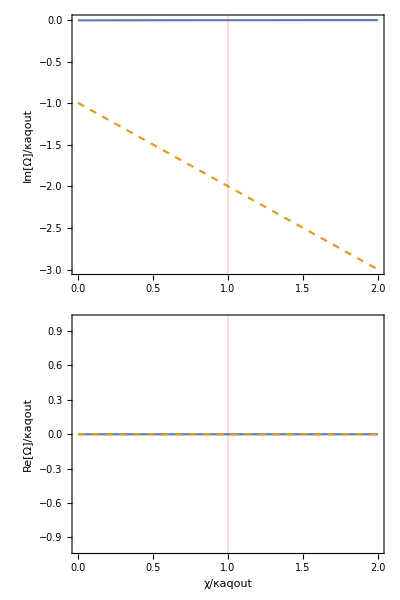

-Graphics-

```mathematica
(*stability of deg. int. sqz., looks stable for all χ, even passed threshold*)
Clear[χ]
denom[Tla_,Tlaq_]:=κaq[Tlaq]+χ-I Ω+ws^2/(κa[Tla]-I Ω);
stabilityIntSqz[Tla_,Tlaq_]:=(
sol=NSolve[denom[Tla,Tlaq]==0,Ω];
p1=Plot[Evaluate[Table[(Im[Ω/.sol[[i]]]/.{χ->ratio κaqout})/κaqout,{i,1,Length[sol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{1,All}},ImageSize->300,Frame->True,FrameLabel->{{"Im[Ω]/κaqout",},{,"poles of transfer function\nunstable when Im[Ω]≥0"}},GridLines->{{{1,Red}},None}];
p2=Plot[Evaluate[Table[(Re[Ω/.sol[[i]]]/.{χ->ratio κaqout})/κaqout,{i,1,Length[sol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{All,1}},ImageSize->300,Frame->True,FrameLabel->{{"Re[Ω]/κaqout",},{"χ/κaqout",}},GridLines->{{{1,Red}},None}];
Column[{p1,p2}])
stabilityIntSqz[0,0]
RegionPlot[Evaluate[Table[(((Im[Ω/.sol[[i]]]/.{χ->ratio κaqout})/κaqout>0)/.{ratio->ratio0})==True,{i,1,Length[imPoles]}]],{ratio0,0,2},{y,0,1},PlotLabel->"is deg. int. sqz. unstable?\ncolour-in if true\n(this plot should be blank)",ImageSize->Small,Frame->True,FrameLabel->{{"(non-axis)",},{"χ/kout",}}]
(*Manipulate[stabilityIntSqz[Tla,Tlaq],{Tla,0,1},{Tlaq,0,1}]*)
```

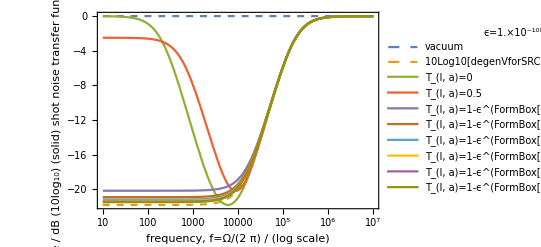

variance DC=-21.8216 dB, shot noise DC=-21.8196 dB

```mathematica
(*comparing shot noise DC to degenerate OPO variance in limit of arm cavity loss -> 1,
does the three mirror system reduce to a two mirror system of the SRM and ITM?*)

(*from OPO .nb, lossy degenerate OPO at either θb=0,π (see that .nb for general angle covariance matrix)*)
degenVforSRC[Ω_,g_,Tloss_:0,Rpd_:0]:=(
(*looking at formal limit of Tla->1, noise in the â mode also shuts off
-- the equivalent of making Titm perfect, not a vacuum port
-- why isn't power still lost through Titm?*)
koutOPO=kout;(*uses Tse and Lse*)
kinOPO=0;(*-1/(2 τRoundTripSE)Log[1-Titm];*)
klossOPO=-1/(2 τRoundTripSE)Log[1-Tloss];
ktotOPO=koutOPO+kinOPO+klossOPO;
1+(4 koutOPO g(1-Rpd))/(Ω^2+(g-ktotOPO)^2))
ϵ=10^-100;
armLossList={1-ϵ,1-ϵ^2,1-ϵ^3,1-ϵ^4,1-ϵ^5,1-ϵ^6};
LogLinearPlot[Evaluate[Join[{
10Log10[1],
10Log10[degenVforSRC[2π f,-χRatio0 kout]],
20Log10[RIntExtSqz[2π f,χRatio0 kout,0,0,0,0,0,0]],
20Log10[RIntExtSqz[2π f,χRatio0 kout,0,0.5,0,0,0,0]]},
Table[
20Log10[RIntExtSqz[2π f,χRatio0 kout,0,armLossList[[i]],0,0,0,0]]
,{i,1,Length[armLossList]}]]],
{f,10,10^7},PlotLegends->LineLegend[Join[{
"vacuum",
"10Log10[degenVforSRC[2π f,-χRatio0 kout]]",
"T_(l, a)=0",
"T_(l, a)=0.5"},
Table[StringForm["T_(l, a)=1-ϵ^(``)",i]
,{i,1,Length[armLossList-1]}]],LabelStyle->Directive[10],LegendLabel->StringForm["ϵ=``",ScientificForm[N[ϵ]]]],PlotRange->All,PlotStyle->{Dashed,Dashed,,,,,,,,},ImageSize->400,Frame->True,FrameLabel->{{ "(dashed) variance / dB (10log_10)\n(solid) shot noise transfer function\n|R| / dB (20log_10)",},{"frequency, f=Ω/(2  π) / (log scale)","deg. int. sqz. reducing to degenerate OPO\nsqueezed quadrature\nusing parameters of reduced two-mirror system (SRM and ITM)\nbut with T_ITM=0 as entire â mode vanishes (this is confusing)"}}]
Print[StringForm["variance DC=`` dB, shot noise DC=`` dB",
NumberForm[10Log10[degenVforSRC[0,-χRatio0 kout]]],

NumberForm[20Log10[RIntExtSqz[0,χRatio0 kout,0,1-ϵ^1000,0,0,0,0]]]]]
(*for χ=χratio0=0.85*)
```

```mathematica
(*split the noise budget
Xpd =(1-Rpd)^(1/2) (T h + Rla Xla + Rlaq Xlaq + Rin Xin)+Rpd^(1/2) Xlpd*)
(*let Internal/External Squeezing be IESqz, these are Abs of fns above*)
RinIESqz[Ω_,χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_]:=(1-Rpd)^(1/2)VExt[Ω,gExt,Rinj,TlExt]^(1/2)Abs[(2κaqout-κaq[Tlaq]-χ+I Ω-ws^2/(κa[Tla]-I Ω))/(κaq[Tlaq]+χ-I Ω+ws^2/(κa[Tla]-I Ω))]
RlaIESqz[Ω_,χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_]:=(1-Rpd)^(1/2)Abs[(2(κaqout κa[Tla])^(1/2)ws)/((κaq[Tlaq]+χ-I Ω)(κa[Tla]-I Ω)+ws^2)]
RlaqIESqz[Ω_,χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_]:=(1-Rpd)^(1/2)Abs[(2(κaqout (κaq[Tlaq]-κaqout))^(1/2))/(κaq[Tlaq]+χ-I Ω+ws^2/(κa[Tla]-I Ω))]
RlpdExtSqz[Ω_,χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_]:=Rpd^(1/2)
(*RIntExtSqz=sum of above four in quadrature*)
(*https://mathematica.stackexchange.com/questions/10833/how-do-i-convert-an-argument-list-to-a-sequence-of-arguments
@@ is infix Apply[f,{a,b,c,d}]*)
noiseBudgetIESqz[params_]:=
LogLinearPlot[{
20Log10[1],
20Log10[RinIESqz@@Join[{2π f},params]],
20Log10[RlaIESqz@@Join[{2π f},params]],
20Log10[RlaqIESqz@@Join[{2π f},params]],
20Log10[RlpdExtSqz@@Join[{2π f},params]],
20Log10[RIntExtSqz@@Join[{2π f},params]]},{f,10,10^5},PlotLegends->LineLegend[{"vacuum","R_in, behind SRM","(R^(L))_a, arm intra-cav.","(R^(L))_aq, SRC intra-cav.","(R^(L))_PD, PD loss","total shot noise"},LabelStyle->Directive[10],LegendLabel->labeller[params]],PlotRange->All,PlotStyle->{Directive[Gray,Dashed],,,,,Directive[Black,Dashed]},Frame->True,FrameLabel->{{"shot noise transfer function,\n|R| / dB (20log10)",},{"frequency, f=Ω/(2  π) / Hz","degenerate internal squeezing\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector"}}]
```

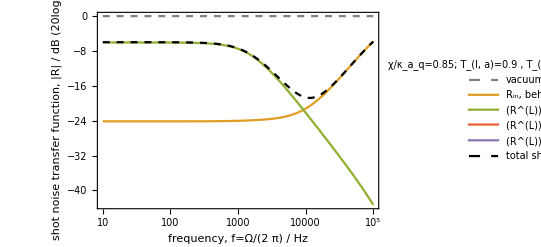

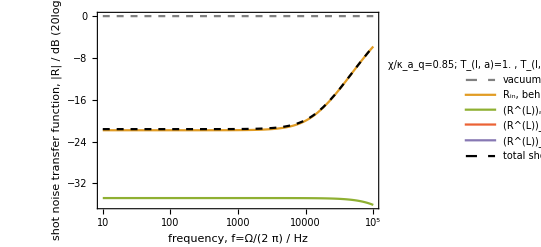

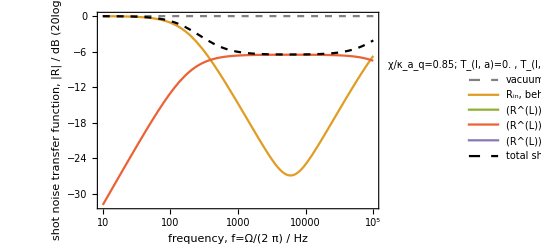

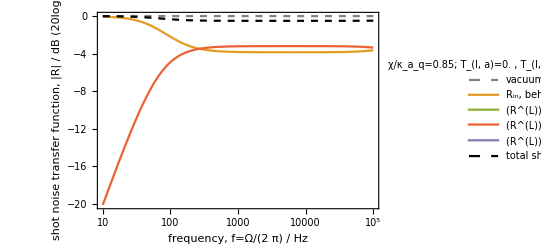

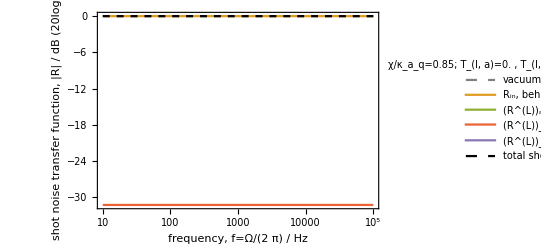

```mathematica
(*understanding Subscript[T, l,a] and Subscript[T, l,aq] behaviour*)
χRatio0=0.85;
noiseBudgetIESqz[{χRatio0 kout,0,0.9,0,0,0,0}]
noiseBudgetIESqz[{χRatio0 kout,0,1-10^-1000,0,0,0,0}]

noiseBudgetIESqz[{χRatio0 kout,0,0,0.1,0,0,0}]
noiseBudgetIESqz[{χRatio0 kout,0,0,0.8,0,0,0}]
noiseBudgetIESqz[{χRatio0 kout,0,0,1-10^-1000,0,0,0}]
```

```mathematica
(*want to find threshold (i.e. point of extremum for shot noise vs. χ) for loss detector, expect to reduce to χ=γR*)
```

```mathematica
$Assumptions={γbtot≥γR>0,ωs>0,Ω≥0,χ≥0,γa≥0,1>Rpd≥0};
FullSimplify[(1-Rpd)(
ComplexExpand[Abs[(2γR-γbtot-χ+I Ω-ωs^2/(γa-I Ω))/(γbtot+χ-I Ω+ωs^2/(γa-I Ω))]^2]
+ComplexExpand[Abs[(2(γR (γbtot-γR))^(1/2))/(γbtot+χ-I Ω+ωs^2/(γa-I Ω))]^2]
+ComplexExpand[Abs[(2(γR γa)^(1/2)ωs)/((γbtot+χ-I Ω)(γa-I Ω)+ωs^2)]^2])+Rpd]
Sx1[Ω_,χ_]:=((γa^2+Ω^2) (4 (-1+Rpd) γR χ+(γbtot+χ)^2+Ω^2)+2 (γa (γbtot+χ)-Ω^2) ωs^2+ωs^4)/((γa^2+Ω^2) ((γbtot+χ)^2+Ω^2)+2 (γa (γbtot+χ)-Ω^2) ωs^2+ωs^4)
DΩSx[Ω_,χ_]:=FullSimplify[D[Sx1[Ω0,χ0],Ω0]/.{Ω0->Ω,χ0->χ}]
DχSx[Ω_,χ_]:=FullSimplify[D[Sx1[Ω0,χ0],χ0]/.{Ω0->Ω,χ0->χ}]
GradSx[Ω_,χ_]:={DΩSx[Ω,χ],DχSx[Ω,χ]}
Sx1[ωs,γbtot]/.{γa->0,Rpd->0,γbtot->γR}//Simplify
DΩSx[ωs,γbtot]/.{γa->0}//Simplify
DχSx[ωs,γbtot]/.{γa->0}//Simplify
```

((γa^2+Ω^2) (γbtot^2+2 γbtot χ+4 (-1+Rpd) γR χ+χ^2+Ω^2)+2 (γa (γbtot+χ)-Ω^2) ωs^2+ωs^4)/((γa^2+Ω^2) ((γbtot+χ)^2+Ω^2)+2 (γa (γbtot+χ)-Ω^2) ωs^2+ωs^4)

0

0

0

```mathematica
(*Solve[{DχSx[Ω,χ]==0,γbtot>=γR>0,ωs>0,Ω>0,γa>=0,1>Rpd>=0},{Ω,χ}]*)sol=Solve[{GradSx[Ω,χ]=={0,0},Ω≥0,χ≥0,γbtot≥γR>0,ωs>0,γa≥0,1>Rpd≥0},{Ω,χ}]//Simplify;
Print["Solve[..., {Ω,χ}] found "<>ToString[Length[sol]]<>" solutions"]
(*Root[f,k]represents the exactk^th root of the polynomial equationf[x]==0.*)
```

Solve[..., {Ω,χ}] found 6 solutions

```mathematica
(sol[[3]]/.{γa->0})//FullSimplify
Solve[(γbtot^3-4 γbtot ωs^2+(-γbtot^2+4 ωs^2) #1-γbtot #1^2+#1^3&)[χ]==0,χ]
Table[Solve[(ωs^4+(γbtot^2-2 ωs^2-(χ/.%[[j]][[1]])^2) #1^2+#1^4&)[Ω]==0,Ω],{j,1,Length[%]}]
```

Power::infy: Infinite expression 1/0 encountered.

Less::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Less::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

{Ω→ConditionalExpression[Root[ωs^4+(γbtot^2-2 ωs^2-Root[γbtot^3-4 γbtot ωs^2+(-γbtot^2+4 ωs^2) #1-γbtot #1^2+#1^3&,2]^2) #1^2+#1^4&,2],Rpd>0&&γbtot>γR&&0<ComplexInfinity&&Root[-ωs^3-3 ωs^2 #1-2 ωs #1^2+2 #1^3&,1]<0&&(0>ComplexInfinity||2 ωs>γbtot)],χ→ConditionalExpression[Root[γbtot^3-4 γbtot ωs^2+(-γbtot^2+4 ωs^2) #1-γbtot #1^2+#1^3&,2],Rpd>0&&γbtot>γR&&0<ComplexInfinity&&Root[-ωs^3-3 ωs^2 #1-2 ωs #1^2+2 #1^3&,1]<0&&(0>ComplexInfinity||2 ωs>γbtot)]}

{{χ→γbtot},{χ→-√(γbtot^2-4 ωs^2)},{χ→√(γbtot^2-4 ωs^2)}}

{{{Ω→-ωs},{Ω→-ωs},{Ω→ωs},{Ω→ωs}},{{Ω→-ⅈ ωs},{Ω→-ⅈ ωs},{Ω→ⅈ ωs},{Ω→ⅈ ωs}},{{Ω→-ⅈ ωs},{Ω→-ⅈ ωs},{Ω→ⅈ ωs},{Ω→ⅈ ωs}}}